# Staged Raw Minimization: (a,c) = (5,1)

This notebook minimizes the main exciton and biexciton with the global-rotation-fixed raw estimator. The exciton kinetic correction is evaluated analytically as alpha^2 (1 + m_e/m_h); only its Coulomb numerator and norm are integrated. The biexciton retains raw G(P+Q), all six Coulomb terms, and all four particle kinetic contributions. The only removed coordinate is the redundant global rotation (phi_a = 0); all three remaining angles cover the full [0,2 Pi] interval. H/V and N use independent AdaptiveQuasiMonteCarlo calls, with no shared fixed points, reflection folding, or particle-exchange multiplicities.

The optimization stage uses 100,000 MaxPoints per integral and warm-starts from the stored reduced-production optimum. The final stage re-evaluates the best low-budget parameters at 2,000,000 MaxPoints. Every integral and objective evaluation is timed and checkpointed. If a minimization is interrupted, evaluate its cell again: it restarts its simplex from the best saved point and reuses any matching completed integrals.

## Load and review configuration

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Main-State-Raw-Minimization-a5-c1.wl"}]]
```

Staged global-rotation-fixed raw minimization loaded at (a,c) = {5.,1.}. Optimization MaxPoints = 100000; final MaxPoints = 2000000. Warm start: <|XAlpha→{0.731089},XXParameters→{0.679864,0.153779,2.49296,2.10885}|>. Run rawMinimizeX[], rawMinimizeXX[], then rawMinFinalize[].

```mathematica
rawMinConfiguration[]
```

<|geometry→{5.,1.},optimizationBudget→100000,finalBudget→2000000,precisionGoal→4,accuracyGoal→∞,bisectionDithering→0,XMaxIterations→30,XXMaxIterations→25,XStartAlpha→0.731089,XXStartParameters→{0.679864,0.153779,2.49296,2.10885},XKinetic→analytic alpha^2 (1 + m_e/m_h),angularTreatment→phi_a=0; all three remaining XX angles cover [0,2 Pi],sampling→independent adaptive QMC calls|>

## Optimize the exciton

This is the cheaper one-parameter minimization. Its objective is the exact analytical kinetic correction plus an independently integrated Coulomb-to-norm ratio.

```mathematica
rawMinimizeX[]
```

optimization / X / normDenominator: 3.43 s

optimization / X / coulombNumerator: 4.88 s

X evaluation 1: alpha = 0.73108941, correction = -2.35227692 Ry

optimization / X / normDenominator: 3.58 s

optimization / X / coulombNumerator: 5.00 s

X evaluation 2: alpha = 0.83108941, correction = -2.337363691 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 3: alpha = 0.73108941, correction = -2.35227692 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 4: alpha = 0.83108941, correction = -2.337363691 Ry

optimization / X / normDenominator: 3.62 s  (reported relative error          -3
3.21 × 10)

optimization / X / coulombNumerator: 4.88 s  (reported relative error          -3
7.22 × 10)

X evaluation 5: alpha = 0.63108941, correction = -2.352903964 Ry

optimization / X / normDenominator: 3.57 s  (reported relative error          -3
2.75 × 10)

optimization / X / coulombNumerator: 4.87 s  (reported relative error          -3
6.61 × 10)

X evaluation 6: alpha = 0.53108941, correction = -2.31238926 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 7: alpha = 0.53108941, correction = -2.31238926 Ry

optimization / X / normDenominator: 3.57 s  (reported relative error          -3
3.45 × 10)

optimization / X / coulombNumerator: 4.84 s  (reported relative error          -3
7.56 × 10)

X evaluation 8: alpha = 0.68108941, correction = -2.360152994 Ry

optimization / X / normDenominator: 3.46 s  (reported relative error          -3
3.68 × 10)

optimization / X / coulombNumerator: 4.83 s  (reported relative error          -3
7.71 × 10)

X evaluation 9: alpha = 0.73108941, correction = -2.35227692 Ry

optimization / X / normDenominator: 3.53 s  (reported relative error          -3
3.33 × 10)

optimization / X / coulombNumerator: 4.84 s  (reported relative error          -3
7.42 × 10)

X evaluation 10: alpha = 0.65608941, correction = -2.362427018 Ry

optimization / X / normDenominator: 3.52 s  (reported relative error          -3
3.21 × 10)

optimization / X / coulombNumerator: 4.87 s  (reported relative error          -3
7.22 × 10)

X evaluation 11: alpha = 0.63108941, correction = -2.352903964 Ry

optimization / X / normDenominator: 3.56 s  (reported relative error          -3
3.39 × 10)

optimization / X / coulombNumerator: 4.99 s  (reported relative error          -3
7.49 × 10)

X evaluation 12: alpha = 0.66858941, correction = -2.358753223 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 13: alpha = 0.66858941, correction = -2.358753223 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 14: alpha = 0.65608941, correction = -2.362427018 Ry

optimization / X / normDenominator: 3.87 s  (reported relative error          -3
3.26 × 10)

optimization / X / coulombNumerator: 5.26 s  (reported relative error          -3
7.24 × 10)

X evaluation 15: alpha = 0.64358941, correction = -2.347231835 Ry

optimization / X / normDenominator: 3.85 s  (reported relative error          -3
3.36 × 10)

optimization / X / coulombNumerator: 5.37 s  (reported relative error          -3
7.44 × 10)

X evaluation 16: alpha = 0.66233941, correction = -2.35994065 Ry

optimization / X / normDenominator: 3.98 s  (reported relative error         -3
3.3 × 10)

optimization / X / coulombNumerator: 5.34 s  (reported relative error          -3
7.34 × 10)

X evaluation 17: alpha = 0.64983941, correction = -2.346501877 Ry

optimization / X / normDenominator: 3.97 s  (reported relative error          -3
3.35 × 10)

optimization / X / coulombNumerator: 5.42 s  (reported relative error          -3
7.37 × 10)

X evaluation 18: alpha = 0.65921441, correction = -2.357010275 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 19: alpha = 0.65921441, correction = -2.357010275 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 20: alpha = 0.65608941, correction = -2.362427018 Ry

optimization / X / normDenominator: 4.01 s  (reported relative error          -3
3.31 × 10)

optimization / X / coulombNumerator: 5.54 s  (reported relative error          -3
7.51 × 10)

X evaluation 21: alpha = 0.65296441, correction = -2.374586569 Ry

optimization / X / normDenominator: 4.10 s  (reported relative error         -3
3.3 × 10)

optimization / X / coulombNumerator: 5.52 s  (reported relative error          -3
7.34 × 10)

X evaluation 22: alpha = 0.64983941, correction = -2.346501877 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 23: alpha = 0.64983941, correction = -2.346501877 Ry

optimization / X / normDenominator: 4.08 s  (reported relative error          -3
3.32 × 10)

optimization / X / coulombNumerator: 5.55 s  (reported relative error          -3
7.44 × 10)

X evaluation 24: alpha = 0.65452691, correction = -2.359189456 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 25: alpha = 0.65296441, correction = -2.374586569 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 26: alpha = 0.65452691, correction = -2.359189456 Ry

optimization / X / normDenominator: 4.05 s  (reported relative error         -3
3.3 × 10)

optimization / X / coulombNumerator: 5.57 s  (reported relative error          -3
7.35 × 10)

X evaluation 27: alpha = 0.65140191, correction = -2.354678393 Ry

optimization / X / normDenominator: 4.07 s  (reported relative error          -3
3.31 × 10)

optimization / X / coulombNumerator: 5.52 s  (reported relative error          -3
7.42 × 10)

X evaluation 28: alpha = 0.65374566, correction = -2.360061816 Ry

optimization / X / normDenominator: 4.02 s  (reported relative error          -3
3.31 × 10)

optimization / X / coulombNumerator: 5.53 s  (reported relative error          -3
7.31 × 10)

X evaluation 29: alpha = 0.65218316, correction = -2.343536874 Ry

optimization / X / normDenominator: 3.99 s  (reported relative error          -3
3.31 × 10)

optimization / X / coulombNumerator: 5.62 s  (reported relative error          -3
7.37 × 10)

X evaluation 30: alpha = 0.65335503, correction = -2.347322154 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 31: alpha = 0.65296441, correction = -2.374586569 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 32: alpha = 0.65335503, correction = -2.347322154 Ry

optimization / X / normDenominator: using checkpointed value

optimization / X / coulombNumerator: using checkpointed value

X evaluation 33: alpha = 0.65296441, correction = -2.374586569 Ry

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.199921 and 0.000640978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.561874 and 0.00405543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.246462 and 0.000677996 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.649782 and 0.00429756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.180915 and 0.000624652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.523406 and 0.00395581 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.164076 and 0.000604149 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.486708 and 0.00375177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.190206 and 0.000633036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.543413 and 0.0040302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.199921 and 0.000640978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.561874 and 0.00405543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.185405 and 0.000629251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.532541 and 0.0039879 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.19487 and 0.000635436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.550139 and 0.00398564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.187715 and 0.00063073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.537606 and 0.00400029 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.19249 and 0.000634397 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.545068 and 0.00400021 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.188928 and 0.000632663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.539632 and 0.00397685 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.191229 and 0.000632763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.547763 and 0.00411593 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.19249 and 0.000634397 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.545068 and 0.00400021 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.190574 and 0.000631999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.543398 and 0.0040445 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.19183 and 0.000633121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.545217 and 0.00400874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.190879 and 0.000631771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.544212 and 0.00403882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.191615 and 0.000633827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.542693 and 0.00396851 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.191124 and 0.00063298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.542362 and 0.00399638 for the integral and error estimates.

<|status→finished,parameters→{0.652964},correctionRy→-2.37459,evaluations→33,budget→100000,completed→2026-07-31T14:44:01|>

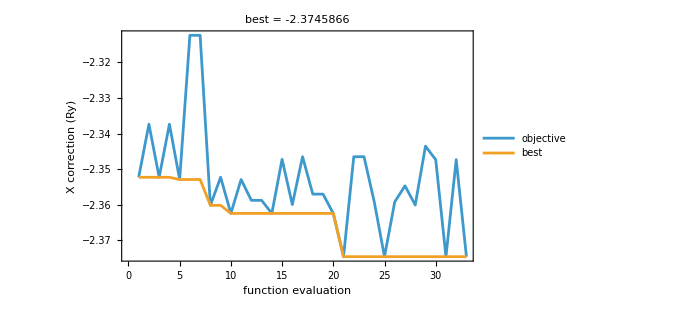

```mathematica
rawMinXConvergencePlot[]
```

## Optimize the biexciton

This is the long stage. At the selected budget, one raw biexciton objective evaluation is expected to take several minutes on the calculation machine. The cell stops at its iteration limit or after the best value stalls, whichever comes first.

```mathematica
rawMinimizeXX[]
```

optimization / XX / normDenominator: 21.14 s

optimization / XX / hamiltonianNumerator: 318.18 s

XX evaluation 1: parameters = {0.6798643,0.1537795,2.492963,2.108847}, correction = -4.853203426 Ry

optimization / XX / normDenominator: 21.04 s

optimization / XX / hamiltonianNumerator: 315.97 s

XX evaluation 2: parameters = {0.8798643,0.1537795,2.492963,2.108847}, correction = -4.68365648 Ry

optimization / XX / normDenominator: 21.33 s

optimization / XX / hamiltonianNumerator: 316.16 s

XX evaluation 3: parameters = {0.6798643,0.3537795,2.492963,2.108847}, correction = -4.563094313 Ry

optimization / XX / normDenominator: 21.00 s

optimization / XX / hamiltonianNumerator: 323.28 s

XX evaluation 4: parameters = {0.6798643,0.1537795,2.692963,2.108847}, correction = -4.827173422 Ry

optimization / XX / normDenominator: 21.08 s

optimization / XX / hamiltonianNumerator: 316.97 s

XX evaluation 5: parameters = {0.6798643,0.1537795,2.492963,2.308847}, correction = -4.930513762 Ry

optimization / XX / normDenominator: using checkpointed value

optimization / XX / hamiltonianNumerator: using checkpointed value

XX evaluation 6: parameters = {0.6798643,0.1537795,2.492963,2.108847}, correction = -4.853203426 Ry

optimization / XX / normDenominator: using checkpointed value

optimization / XX / hamiltonianNumerator: using checkpointed value

XX evaluation 7: parameters = {0.8798643,0.1537795,2.492963,2.108847}, correction = -4.68365648 Ry

optimization / XX / normDenominator: using checkpointed value

optimization / XX / hamiltonianNumerator: using checkpointed value

XX evaluation 8: parameters = {0.6798643,0.3537795,2.492963,2.108847}, correction = -4.563094313 Ry

optimization / XX / normDenominator: using checkpointed value

optimization / XX / hamiltonianNumerator: using checkpointed value

XX evaluation 9: parameters = {0.6798643,0.1537795,2.692963,2.108847}, correction = -4.827173422 Ry

optimization / XX / normDenominator: using checkpointed value

optimization / XX / hamiltonianNumerator: using checkpointed value

XX evaluation 10: parameters = {0.6798643,0.1537795,2.492963,2.308847}, correction = -4.930513762 Ry

optimization / XX / normDenominator: 21.11 s

optimization / XX / hamiltonianNumerator: 320.81 s  (reported relative error          -2
1.17 × 10)

XX evaluation 11: parameters = {0.7798643,0.06524678,2.592963,2.208847}, correction = -4.787321976 Ry

optimization / XX / normDenominator: 20.97 s

optimization / XX / hamiltonianNumerator: 315.73 s  (reported relative error          -3
9.95 × 10)

XX evaluation 12: parameters = {0.5298643,0.1095131,2.642963,2.258847}, correction = -4.859737343 Ry

optimization / XX / normDenominator: 20.89 s

optimization / XX / hamiltonianNumerator: 315.95 s  (reported relative error          -2
1.07 × 10)

XX evaluation 13: parameters = {0.5048643,0.220179,2.567963,2.183847}, correction = -4.907069762 Ry

optimization / XX / normDenominator: 21.11 s

optimization / XX / hamiltonianNumerator: 316.40 s  (reported relative error          -2
1.11 × 10)

XX evaluation 14: parameters = {0.5173643,0.1648461,2.405463,2.321347}, correction = -4.80051746 Ry

optimization / XX / normDenominator: 20.92 s

optimization / XX / hamiltonianNumerator: 316.63 s  (reported relative error         -2
1.1 × 10)

XX evaluation 15: parameters = {0.6392393,0.1565461,2.621088,2.161972}, correction = -4.91410933 Ry

optimization / XX / normDenominator: 21.09 s

optimization / XX / hamiltonianNumerator: 315.91 s  (reported relative error          -2
1.04 × 10)

XX evaluation 16: parameters = {0.4970518,0.1662294,2.669526,2.347909}, correction = -4.85102818 Ry

optimization / XX / normDenominator: 21.10 s

optimization / XX / hamiltonianNumerator: 322.51 s  (reported relative error          -2
1.12 × 10)

XX evaluation 17: parameters = {0.6341612,0.156892,2.537104,2.168612}, correction = -4.836300246 Ry

optimization / XX / normDenominator: 21.45 s

optimization / XX / hamiltonianNumerator: 329.91 s  (reported relative error          -2
1.17 × 10)

XX evaluation 18: parameters = {0.6798643,0.1537795,2.492963,2.208847}, correction = -4.813625048 Ry

optimization / XX / normDenominator: 21.49 s

optimization / XX / hamiltonianNumerator: 319.86 s  (reported relative error          -2
1.11 × 10)

XX evaluation 19: parameters = {0.6048643,0.1316463,2.567963,2.283847}, correction = -4.787342209 Ry

optimization / XX / normDenominator: 21.12 s

optimization / XX / hamiltonianNumerator: 319.48 s  (reported relative error          -2
1.14 × 10)

XX evaluation 20: parameters = {0.5923643,0.1869793,2.530463,2.246347}, correction = -4.889688388 Ry

optimization / XX / normDenominator: 21.10 s

optimization / XX / hamiltonianNumerator: 317.18 s  (reported relative error          -2
1.16 × 10)

XX evaluation 21: parameters = {0.6595518,0.1551628,2.557026,2.235409}, correction = -4.895081718 Ry

optimization / XX / normDenominator: using checkpointed value

optimization / XX / hamiltonianNumerator: using checkpointed value

XX evaluation 22: parameters = {0.6798643,0.1537795,2.492963,2.308847}, correction = -4.930513762 Ry

optimization / XX / normDenominator: 21.74 s

optimization / XX / hamiltonianNumerator: 318.99 s  (reported relative error          -2
1.25 × 10)

XX evaluation 23: parameters = {0.700958,0.1932042,2.468745,2.215878}, correction = -4.871526366 Ry

optimization / XX / normDenominator: 20.81 s

optimization / XX / hamiltonianNumerator: 319.63 s  (reported relative error          -2
1.19 × 10)

XX evaluation 24: parameters = {0.6365049,0.1907834,2.531635,2.294394}, correction = -4.798631157 Ry

optimization / XX / normDenominator: 20.98 s

optimization / XX / hamiltonianNumerator: 318.82 s  (reported relative error          -2
1.17 × 10)

XX evaluation 25: parameters = {0.6690245,0.1630305,2.502631,2.230233}, correction = -4.845528293 Ry

optimization / XX / normDenominator: 21.63 s

optimization / XX / hamiltonianNumerator: 319.94 s  (reported relative error          -2
1.19 × 10)

XX evaluation 26: parameters = {0.6473448,0.1815324,2.521967,2.273007}, correction = -4.891522291 Ry

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000450318 and 3.18168×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00215582 and 0.0000252593 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000920195 and 5.37368×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00447191 and 0.0000445078 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000717605 and 4.51982×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00352134 and 0.000037581 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000611771 and 3.97479×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00293682 and 0.0000326135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000584208 and 3.86686×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00287086 and 0.0000314463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.00065806 and 3.98634×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00319227 and 0.0000331594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000575204 and 3.84067×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00278186 and 0.0000312144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000432798 and 3.04956×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00208333 and 0.000024419 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000556027 and 3.6136×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00266189 and 0.000029474 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.00049169 and 3.36705×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00240421 and 0.0000274791 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000444332 and 3.1013×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00217504 and 0.0000251257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000326472 and 2.44858×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00159042 and 0.0000199384 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000360203 and 2.59111×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00172848 and 0.0000206335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000412838 and 2.93045×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00200042 and 0.0000234374 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained 0.000376424 and 2.70228×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 100100 integrand evaluations. NIntegrate obtained -0.00184128 and 0.0000218493 for the integral and error estimates.

optimization / XX / normDenominator: using checkpointed value

optimization / XX / hamiltonianNumerator: using checkpointed value

XX evaluation 27: parameters = {0.6798643,0.1537795,2.492963,2.108847}, correction = -4.853203426 Ry

optimization / XX / normDenominator: using checkpointed value

optimization / XX / hamiltonianNumerator: using checkpointed value

XX evaluation 28: parameters = {0.8798643,0.1537795,2.492963,2.108847}, correction = -4.68365648 Ry

optimization / XX / normDenominator: using checkpointed value

optimization / XX / hamiltonianNumerator: using checkpointed value

XX evaluation 29: parameters = {0.6798643,0.3537795,2.492963,2.108847}, correction = -4.563094313 Ry

optimization / XX / normDenominator: using checkpointed value

optimization / XX / hamiltonianNumerator: using checkpointed value

XX evaluation 30: parameters = {0.6798643,0.1537795,2.692963,2.108847}, correction = -4.827173422 Ry

optimization / XX / normDenominator: using checkpointed value

optimization / XX / hamiltonianNumerator: using checkpointed value

XX evaluation 31: parameters = {0.6798643,0.1537795,2.492963,2.308847}, correction = -4.930513762 Ry

<|status→stalled,parameters→{0.679864,0.153779,2.49296,2.30885},correctionRy→-4.93051,evaluations→31,budget→100000,completed→2026-07-31T16:37:27|>

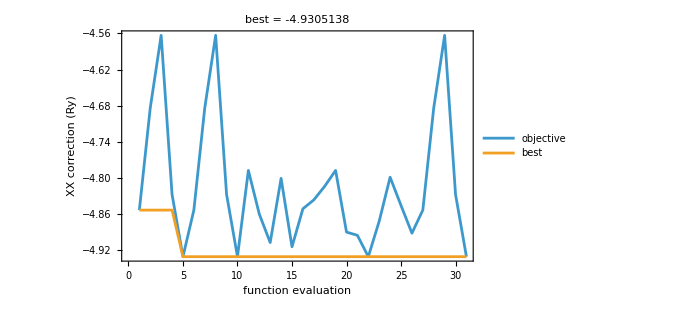

```mathematica
rawMinXXConvergencePlot[]
```

## High-budget final evaluation

Run this only after both minimizations have produced histories. It evaluates the best saved X and XX parameters at 2,000,000 MaxPoints and assembles the corrected total energies and binding energy.

```mathematica
rawMinFinalize[]
```

Final evaluation at MaxPoints = 2000000. X alpha = 0.652964; XX parameters = {0.679864,0.153779,2.49296,2.30885}

final / X / normDenominator: 80.75 s  (reported relative error          -4
7.45 × 10)

final / X / coulombNumerator: 110.06 s  (reported relative error          -3
1.63 × 10)

final / XX / normDenominator: 436.29 s

final / XX / hamiltonianNumerator: 6375.53 s

<|geometry→<|a→5.,c→1.|>,optimizationBudget→100000,finalBudget→2000000,X→<|system→X,evaluation→34,budget→2000000,parameters→{0.652964},parameterKey→0.6529644085677733,norm→0.191172,numeratorRy→-0.543248,analyticKineticRy→0.489843,correctionRy→-2.35183,elapsedSeconds→190.894,completed→2026-07-31T16:40:38,alpha→0.652964,singleParticleRy→12.7828,totalRy→10.431|>,XX→<|system→XX,evaluation→32,budget→2000000,parameters→{0.679864,0.153779,2.49296,2.30885},parameterKey→0.6798642956307124|0.15377949033301186|2.492963267977676|2.308846628792432,norm→0.00034472,numeratorRy→-0.00166373,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.82632,elapsedSeconds→6811.9,completed→2026-07-31T18:34:10,singleParticleRy→25.5656,totalRy→20.7393|>,bindingRy→0.122658,completed→2026-07-31T18:34:10|>

## Saved summary

```mathematica
rawMinSummary[]
```

<|configuration→<|geometry→{5.,1.},optimizationBudget→100000,finalBudget→2000000,precisionGoal→4,accuracyGoal→∞,bisectionDithering→0,XMaxIterations→30,XXMaxIterations→25,XStartAlpha→0.731089,XXStartParameters→{0.679864,0.153779,2.49296,2.10885},XKinetic→analytic alpha^2 (1 + m_e/m_h),angularTreatment→phi_a=0; all three remaining XX angles cover [0,2 Pi],sampling→independent adaptive QMC calls|>,XBestLowBudget→<|system→X,evaluation→21,budget→100000,parameters→{0.652964},parameterKey→0.6529644085677733,norm→0.191229,numeratorRy→-0.547763,analyticKineticRy→0.489843,correctionRy→-2.37459,elapsedSeconds→9.61656,completed→2026-07-31T14:43:03|>,XXBestLowBudget→<|system→XX,evaluation→5,budget→100000,parameters→{0.679864,0.153779,2.49296,2.30885},parameterKey→0.6798642956307124|0.15377949033301186|2.492963267977676|2.308846628792432,norm→0.000341062,numeratorRy→-0.00168161,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.93051,elapsedSeconds→338.087,completed→2026-07-31T15:12:18|>,optimizationResults→<|X→<|status→finished,parameters→{0.652964},correctionRy→-2.37459,evaluations→33,budget→100000,completed→2026-07-31T14:44:01|>,XX→<|status→stalled,parameters→{0.679864,0.153779,2.49296,2.30885},correctionRy→-4.93051,evaluations→31,budget→100000,completed→2026-07-31T16:37:27|>|>,finalResult→<|geometry→<|a→5.,c→1.|>,optimizationBudget→100000,finalBudget→2000000,X→<|system→X,evaluation→34,budget→2000000,parameters→{0.652964},parameterKey→0.6529644085677733,norm→0.191172,numeratorRy→-0.543248,analyticKineticRy→0.489843,correctionRy→-2.35183,elapsedSeconds→190.894,completed→2026-07-31T16:40:38,alpha→0.652964,singleParticleRy→12.7828,totalRy→10.431|>,XX→<|system→XX,evaluation→32,budget→2000000,parameters→{0.679864,0.153779,2.49296,2.30885},parameterKey→0.6798642956307124|0.15377949033301186|2.492963267977676|2.308846628792432,norm→0.00034472,numeratorRy→-0.00166373,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.82632,elapsedSeconds→6811.9,completed→2026-07-31T18:34:10,singleParticleRy→25.5656,totalRy→20.7393|>,bindingRy→0.122658,completed→2026-07-31T18:34:10|>,integralCount→84,XEvaluationCount→33,XXEvaluationCount→31|>